```mathematica
CalcMinGraphs[g_,faces_,stopAt_]:=Block[{face,i,newFaces,h,newVertex,result={}},
If[stopAt==0,
{g},
newVertex=Max[VertexList[g]]+1;
For[i=1,i≤Length[faces],i++,
face=faces[[i]];
h=EdgeAdd[g,face[[1]]<->newVertex];
h=EdgeAdd[h,face[[2]]<->newVertex];
h=EdgeAdd[h,face[[3]]<->newVertex];
newFaces=Join[faces,{{face[[1]],face[[2]],newVertex},{face[[3]],face[[2]],newVertex},{face[[1]],face[[3]],newVertex}}];
result=Join[result,CalcMinGraphs[h,newFaces,stopAt-1]]
];
result
]
]
```

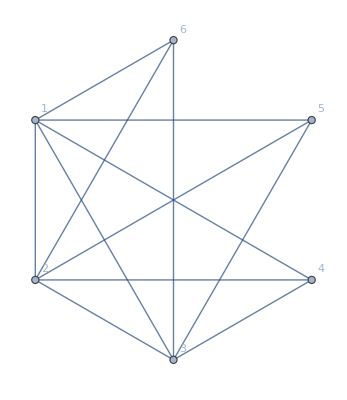
```mathematica
FindFullFormula[-Graphics-]
```

{v1x2x3x4x5x6,v1x2x3x4x56,v1x2x3x46x5,v1x2x3x45x6,v1x2x3x456}

```mathematica
Table[Length[Tally[CalcMinGraphs[CompleteGraph[3,VertexLabels->"Name"],{{1,2,3}},l],IsomorphicGraphQ]],{l,1,7}]
```

{1,1,2,5,15,58,275}

```mathematica
Table[Length[CalcMinGraphs[CompleteGraph[3,VertexLabels->"Name"],{{1,2,3}},l]//DeleteDuplicates],{l,1,6}]
```

{1,4,28,280,3640,58240}

```mathematica
CountFor[set_,c_]:=Length[Select[set,StringCount[SymbolName[#],"x"]+1==c&]]
```

```mathematica
CountFor[{v1x2x3x4x5x6x7,v1x2x3x4x5x67,v1x2x3x4x57x6,v1x2x3x4x56x7,v1x2x3x4x567,v1x2x3x47x5x6,v1x2x3x47x56,v1x2x3x46x5x7,v1x2x3x467x5,v1x2x3x46x57,v1x2x3x45x6x7,v1x2x3x457x6,v1x2x3x456x7,v1x2x3x45x67,v1x2x3x4567},4]
```

1

```mathematica
start=0;fors=Monitor[Table[start+=1;FindFullFormula[gg],{gg,CalcMinGraphs[CompleteGraph[3,VertexLabels->"Name"],{{1,2,3}},5]}],start];
```

```mathematica
Table[Table[CountFor[f,k],{k,1,10}],{f,fors}]//Tally
```

{{{0,0,0,1,15,25,10,1,0,0},3640}}

```mathematica
Select[%,#[[2]]≠1&]
```

{{{0,0,0,1,15,25,10,1,0,0},3640}}

```mathematica
start=0;fors=Monitor[Table[start+=1;FindFullFormula[gg],{gg,CalcMinGraphs[CompleteGraph[3,VertexLabels->"Name"],{{1,2,3}},6]}],start];
```

```mathematica
Table[Table[CountFor[f,k],{k,1,10}],{f,fors}]//Tally
```

{{{0,0,0,1,31,90,65,15,1,0},58240}}

```mathematica
Select[%,#[[2]]≠1&]
```

{{{0,0,0,1,31,90,65,15,1,0},58240}}

```mathematica
start=0;fors=Monitor[Table[start+=1;FindFullFormula[gg],{gg,CalcMinGraphs[CompleteGraph[3,VertexLabels->"Name"],{{1,2,3}},7]}],start];
```

```mathematica
Table[Table[CountFor[f,k],{k,1,11}],{f,fors}]//Tally
```

{{{0,0,0,1,31,90,65,15,1,0},58240}}